# T_H und C-Plots

```mathematica
ArcTan@HoloGraphs[4]π//N
```

{0.769623,-4.92889,-4.93262,-4.93421,-4.93466,-4.93477,-4.93479,-4.9348,-4.9348}

```mathematica
(* Labels direkt auf Funktionen anzeigen *)
ClearAll[EpiLabels]
EpiLabels[xpoint_,data_, labels_]:= 
Text[
Rotate[labels[[#]],ArcTan[ data'[xpoint][[#]] ]],
{xpoint, 0 + data[xpoint][[#]]},
Background -> White
(* Opacity[0.8,White]*)
] & /@ Range@Length[data[1]] (* 1: any value to introspect list*)
```

```mathematica
(* Generic Functions *)
ClearAll[T,CC,M]
(* Hawking-Temperatur. T*L = Einheitslos *)
T[H_,zH_,n_] = 1/L *1/(4 Pi zH) * (1 + n - zH * (D[H[x],x]/. {x-> zH})/H[zH]);
(* Heat capacity (CC weil C[] in Mathematica reserviert ist) *)
(* A = (n+2)/2 MΩZeug *)
M[H_,zH_,n_] =1/A* 1/H[zH] (zH/L)^(n+1);
(* CC * A L^n = Einheitslos *)
CC[H_,zH_,n_] = D[M[H,zH,n],zH]*1/D[T[H,zH,n],zH] // FullSimplify;
```

## Holo-Function n dim

```mathematica
ClearAll[h,HoloGraphs]
(* holographisches Modell *)
h[z_] := 1/(1+(1/z)^(2+n));
Subscript[r, 0]=(1/(1+n))^(1/(2+n));
(* Skalierte Variablen: x = zH/r0  mit r0 = r0(n) dem Extremal Radius.
Auf diese WeHoloLabelsise gilt für alle Temperaturen: T(1) =0! :D *)
HoloGraphs[x_] = Join[{1/x},Table[L * T[h, x *Subscript[r, 0],n], {n,0,7}]]
HoloLabels = Join[{"Schwarzschild"}, Table["n="<>ToString[n],{n,0,7}]];
```

{1/x,(1-2/((1+1/x^2) x^2))/(4 π x),(2-6/((1+2/x^3) x^3))/(2 2^(2/3) π x),(3^(1/4) (3-12/((1+3/x^4) x^4)))/(4 π x),(4-20/((1+4/x^5) x^5))/(2 2^(3/5) π x),(5^(1/6) (5-30/((1+5/x^6) x^6)))/(4 π x),(3^(1/7) (6-42/((1+6/x^7) x^7)))/(2 2^(6/7) π x),(7^(1/8) (7-56/((1+7/x^8) x^8)))/(4 π x),(8-72/((1+8/x^9) x^9))/(2 2^(2/3) π x)}

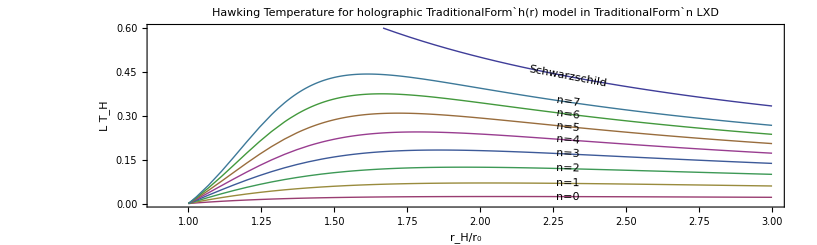

```mathematica
Plot[Evaluate[HoloGraphs[x]],{x,0.9,3},PlotRange->{0,0.6},(*PlotLegends->Placed[Join@@{{"Schwarzschild"},Table["n="<>ToString[n],{n,0,7}]},{Left,Bottom}],*)Frame->True,FrameLabel->{"r_H/r_0","L T_H"},AspectRatio->0.3,PlotLabel->"Hawking Temperature for holographic \!\(TraditionalForm\`\(\(h\)\((\)\(r\)\)\)) model in \!\(TraditionalForm\`n\) LXD",Epilog->EpiLabels[2.3,HoloGraphs, HoloLabels]]
```

## Combined Plot h ∧h_α Functions ndim

```mathematica
(* hAlpha Self Regular Modell *)
ClearAll[HaGraphs, HaLabels]
Subscript[α, 0]=(3+n)/Log[2+n] * Log[(3+n)/2];
Subscript[r, 0,α]=(1/(1+n))^(1/Subscript[α, 0]);
hA[z_] = 1/(1+(1/z)^Subscript[α, 0] / 2)^((3+n)/Subscript[α, 0]);
(* Skalierte Variablen: x = zH/r0  mit r0 = r0(n) dem Extremal Radius.
Auf diese Weise gilt für alle Temperaturen: T(1) =0! :D *)
HaGraphs[x_] = Table[L * T[hA,x *Subscript[r, 0,α],n], {n,0,7}];
HaLabels = Table["Self-Regular n="<>ToString[n],{n,0,7}];
HoloLabels = Join[{"Schwarzschild"}, Table["Holo n="<>ToString[n],{n,0,7}]];
```

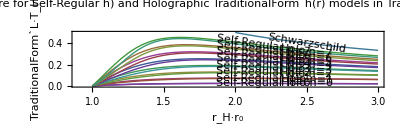

```mathematica
Plot[Evaluate[Join[HaGraphs[x],HoloGraphs[x]]], {x, 0.9, 3}, PlotRange -> {0, 0.5}, 
  Frame -> True, FrameLabel -> {"r_H·r_0", "TraditionalForm`L·T_H"},
  AspectRatio ->  1/3,ImageSize-> Full,
 PlotLabel ->  "Hawking Temperature for Self-Regular h) and Holographic TraditionalForm`h(r) models in TraditionalForm`n+4 dimensions",
Epilog ->  Join[EpiLabels[2.2,HaGraphs, HaLabels],EpiLabels[2.5, HoloGraphs, HoloLabels]]]
(*HoloMaxs = Table[FindMaximum[{L*T[h,x,n],1≤x≤3},{x,2}],{n,0,7}]/. { ({y_,{x-> xval_}}) -> {xval,y}}
p2= ListPlot[HoloMaxs]
Show[p1,p2]*)
```

## Critical Radii

```mathematica
(* Bestimme die kritischen Radii, vgl. das zugehoerige Worksheet *)
HoloTMaxima = Table[FindMaximum[{L*T[h,x*Subscript[r, 0],n],1≤x≤3},{x,2}],{n,0,7}];
HalphaTMaxima = Table[FindMaximum[ {L*T[hA,x*Subscript[r, 0,α],n],1≤ x≤ 3},{x,2}],{n,0,7}];
```

```mathematica
(* Zum Listplot *)
HoloTXY = HoloTMaxima /. { ({y_,{x-> xval_}}) -> {xval,y}};
HalphaTXY = HalphaTMaxima/. { ({y_,{x-> xval_}}) -> {xval,y}};
```

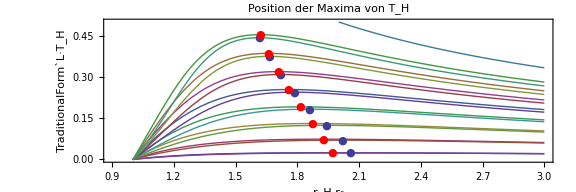

```mathematica
p1 = Plot[Evaluate[Join[HaGraphs[x],HoloGraphs[x]]], {x, 0.9, 3}, PlotRange -> {0, 0.5}, 
  Frame -> True, FrameLabel -> {"r_H·r_0", "TraditionalForm`L·T_H"},
 AspectRatio ->  1/3,ImageSize-> Large,
 PlotLabel ->  "Position der Maxima von T_H"
];
p2= ListPlot[HoloTXY,PlotMarkers-> {Automatic, Medium}];
p3 = ListPlot[HalphaTXY,PlotMarkers-> {Automatic, Medium},PlotStyle-> Red];
Show[p1,p2,p3]
```

```mathematica
(* Die Subscript[r, C] kritischen Raddi zum Skalierender Heat Capacity *)
HoloCriticals =  HoloTMaxima /. { ({y_,{x-> xval_}}) -> xval};
HalphaCriticals = HalphaTMaxima /. { ({y_,{x-> xval_}}) -> xval};
```

## Heat Capacity

```mathematica
(* Shiftet data around Criticals *)
nValues = {0,1,2,4,7};
HaGraphs[x_] = Table[A*L^n * CC[hA,(x+HalphaCriticals[[n+1]]) *Subscript[r, 0,α],n], {n,nValues}];
HoloGraphs[x_] = Table[A*L^n*CC[h,(x+HoloCriticals[[n+1]])*Subscript[r, 0],n],{n,nValues}];
```

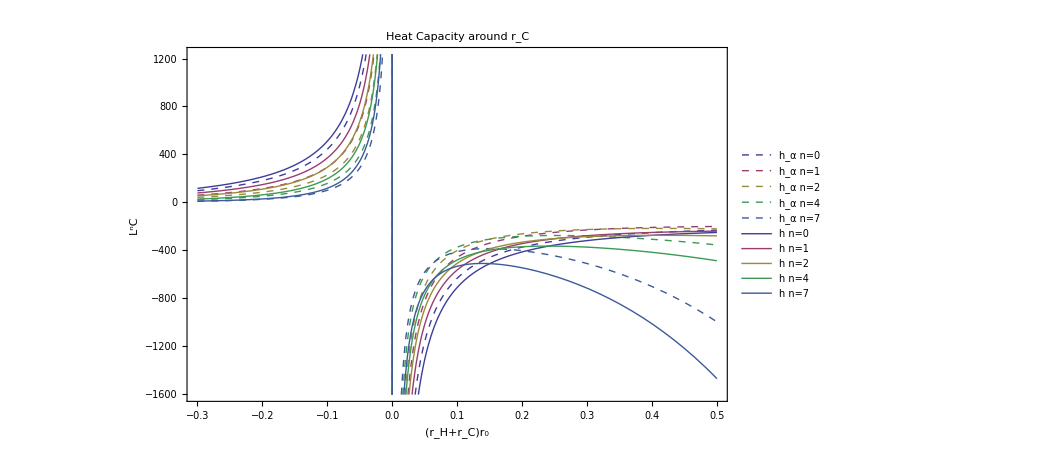

```mathematica
(* Make some shitty plot *)
Plot[Evaluate[Join[HaGraphs[x],HoloGraphs[x]]], {x,-.3,.5}, Frame-> True,
PlotLabel-> "Heat Capacity around r_C",
FrameLabel -> {"(r_H+r_C)r_0", "L^nC"},
PlotStyle-> {{ColorData[1][1],Dashed}, {ColorData[1][2],Dashed}, {ColorData[1][3],Dashed}, {ColorData[1][4],Dashed}, {ColorData[1][5],Dashed}, {ColorData[1][1]},{ColorData[1][2]},{ColorData[1][3]},{ColorData[1][4]},{ColorData[1][5]}},
PlotLegends->Placed[Join[
Table["h_α n="<>ToString[n],{n,nValues}],
Table["h n="<>ToString[n],{n,nValues}]
],{Left,Bottom}]]
```

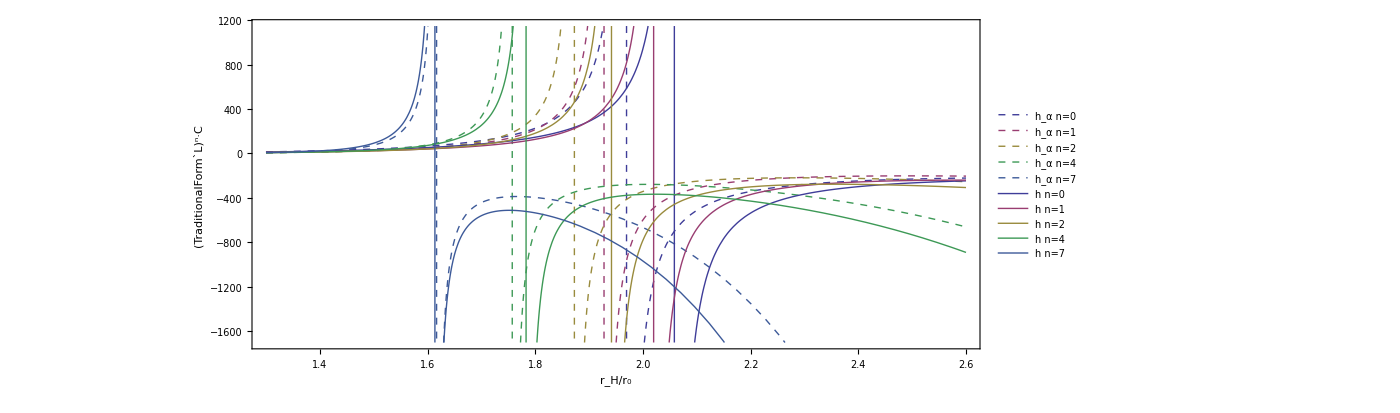

```mathematica
(* Non-Shiftet versions *)
nValues = {0,1,2,4,7};
NonHaGraphs[x_] = Table[A*L^n * CC[hA,x*Subscript[r, 0,α],n], {n,nValues}];
NonHoloGraphs[x_] = Table[A*L^n*CC[h,x*Subscript[r, 0],n],{n,nValues}];

Plot[Evaluate[Join[NonHaGraphs[x], NonHoloGraphs[x]]], {x, 1.3, 2.6},
PlotStyle-> {{ColorData[1][1],Dashed}, {ColorData[1][2],Dashed}, {ColorData[1][3],Dashed}, {ColorData[1][4],Dashed}, {ColorData[1][5],Dashed}, {ColorData[1][1]},{ColorData[1][2]},{ColorData[1][3]},{ColorData[1][4]},{ColorData[1][5]}},
  Frame -> True, FrameLabel -> {"r_H/r_0", "(TraditionalForm`L)^n·C"},
PlotLegends->Placed[Join[
Table["h_α n="<>ToString[n],{n,nValues}],
Table["h n="<>ToString[n],{n,nValues}]
],{Left,Bottom}],
AspectRatio->1/2.5
]
```